```mathematica
data=Import["C:\\Users\\62472\\Desktop\\nasa.xlsx"];
```

```mathematica
actualdata=Table[Table[Table[0,117],117],16];
```

```mathematica
For[k=1,k<17,k++,
For[i=1,i<118,i++,
For[j=1,j<118,j++,
actualdata[[k,i,j]]=data[[k,i+2165,j+1963]]
]
]
]
```

```mathematica
ave=Table[Table[Table[0,117],117],4];
```

```mathematica
For[i=1,i<5,i++,
ave[[i]]=Sum[actualdata[[(i-1)*4+j]],{j,1,3}]/3]
```

```mathematica
Length[ave]
```

4

```mathematica
Mean[Mean[(ave[[2]]-ave[[1]])/ave[[1]]]]
```

-0.10601

```mathematica
Mean[Mean[(ave[[4]]-ave[[3]])/ave[[3]]]]
```

0.279691

```mathematica
dif03=(ave[[2]]-ave[[1]])/ave[[1]];
dif20=(ave[[4]]-ave[[3]])/ave[[3]];
```

```mathematica
coordOfIncrease03={};
coordOfIncrease20={};
For[i=1,i≤Length[ave[[1]]],i++,
For[j=1,j≤Length[ave[[1,1]]],j++,
If[dif03[[i,j]]>=0.,AppendTo[coordOfIncrease03,{{i,j},dif03[[i,j]]}]];
If[dif20[[i,j]]>=0.,AppendTo[coordOfIncrease20,{{i,j},dif20[[i,j]]}]];
]
]
```

```mathematica
Length[coordOfIncrease20]/(117*117.)
```

0.35744

```mathematica
Length[coordOfIncrease03]/(117*117.)
```

0.0000730514

```mathematica
Length[ave[[1]]]
```

117

```mathematica
a={0,0,0};
```

```mathematica
Append[a,{1}]
```

{0,0,0,{1},{1}}

```mathematica
a
```

{0,0,0,{1}}

```mathematica
Mean[Mean[ave[[3]]]]
```

1116.75

```mathematica
Length[ave]
```

4

```mathematica
Mean[ave[[1]]]
```

{2559.6,2554.77,2535.54,2520.81,2513.06,2503.88,2486.52,2477.29,2488.99,2481.17,2464.47,2453.06,2475.71,2468.24,2478.88,2476.53,2489.51,2483.95,2504.58,2509.26,2493.56,2502.43,2506.68,2497.95,2516.75,2515.93,2527.67,2523.58,2542.6,2549.27,2536.65,2539.64,2541.87,2557.35,2573.86,2578.47,2596.93,2622.04,2616.75,2654.82,2664.68,2660.41,2671.19,2674.43,2645.48,2671.91,2662.05,2690.2,2686.24,2696.48,2679.35,2692.84,2694.62,2702.83,2734.63,2760.35,2764.52,2799.48,2788.55,2782.09,2804.19,2811.03,2794.53,2793.05,2793.03,2821.59,2825.39,2832.43,2829.14,2861.32,2838.68,2890.62,2888.64,2888.66,2911.56,2954.31,2972.28,2988.39,2993.42,2995.43,3001.55,2993.56,2961.27,2975.8,2959.54,2969.44,2993.65,3021.04,3005.12,3014.21,3044.93,3053.49,3069.13,3103.18,3107.72,3132.52,3142.1,3164.93,3161.84,3178.51,3169.32,3187.51,3187.89,3212.74,3249.96,3260.72,3268.65,3270.54,3258.65,3245.75,3243.02,3228.01,3221.04,3209.18,3202.43,3188.59,3184.23}

```mathematica
meandata=Table[Mean[Mean[actualdata[[i]]]],{i,1,Length[actualdata]}];
```

```mathematica
For[i=1,i≤Length[actualdata],i++,
Print[Mean[Mean[actualdata[[i]]]]]
]
```

939.67

1023.31

2101.52

7161.91

1232.21

996.258

1010.18

941.172

828.149

849.235

862.244

1927.36

1439.97

835.013

973.848

884.57

```mathematica
meandata
```

1232.21

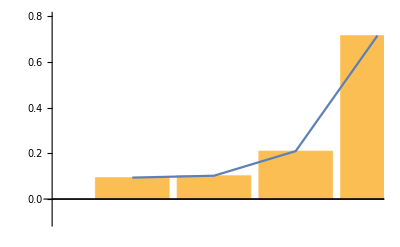

```mathematica
Show[BarChart[10^-4*Table[meandata[[i]],{i,1,4}]],ListLinePlot[10^-4*Table[meandata[[i]],{i,1,4}]],PlotRange->{{0,4},{-.1,.8}}]
```

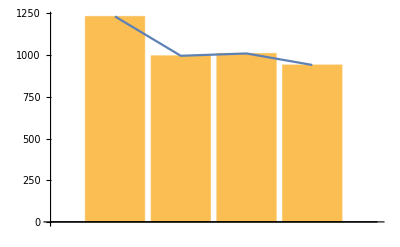

```mathematica
Show[BarChart[Table[meandata[[i]],{i,5,8}]],ListLinePlot[Table[meandata[[i]],{i,5,8}]]]
```

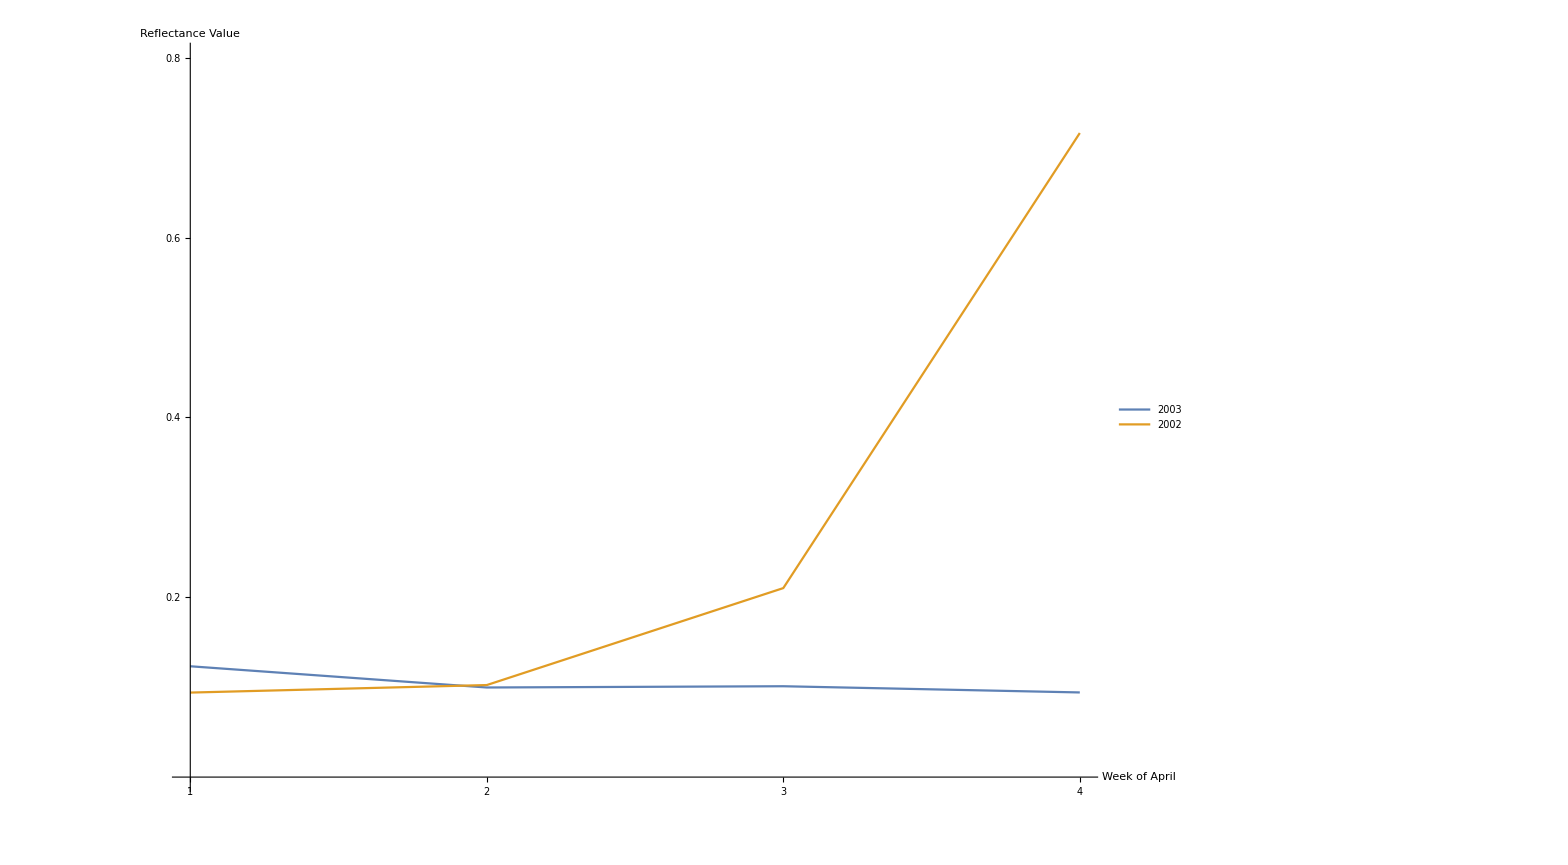

```mathematica
ListLinePlot[{10^-4*Table[meandata[[i]],{i,5,8}],10^-4*Table[meandata[[i]],{i,1,4}]},AxesOrigin->{1,0},PlotLegends->{"2003","2002"},PlotRange->{Full,{0,.8}},AxesLabel->{"Week of April","Reflectance Value"},LabelStyle->Directive[Bold,FontFamily->"Times New Roman",35],Ticks->{{1,2,3,4},{0.2,0.4,0.6,0.8}},ImageSize->1400,TicksStyle->Large]
```

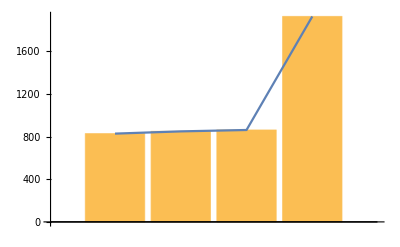

```mathematica
Show[BarChart[Table[meandata[[i]],{i,9,12}]],ListLinePlot[Table[meandata[[i]],{i,9,12}]]]
```

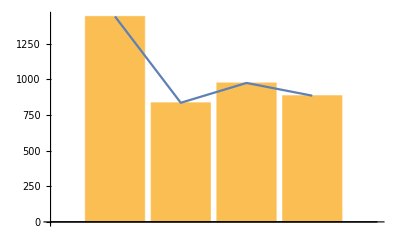

```mathematica
Show[BarChart[Table[meandata[[i]],{i,13,16}]],ListLinePlot[Table[meandata[[i]],{i,13,16}]]]
```

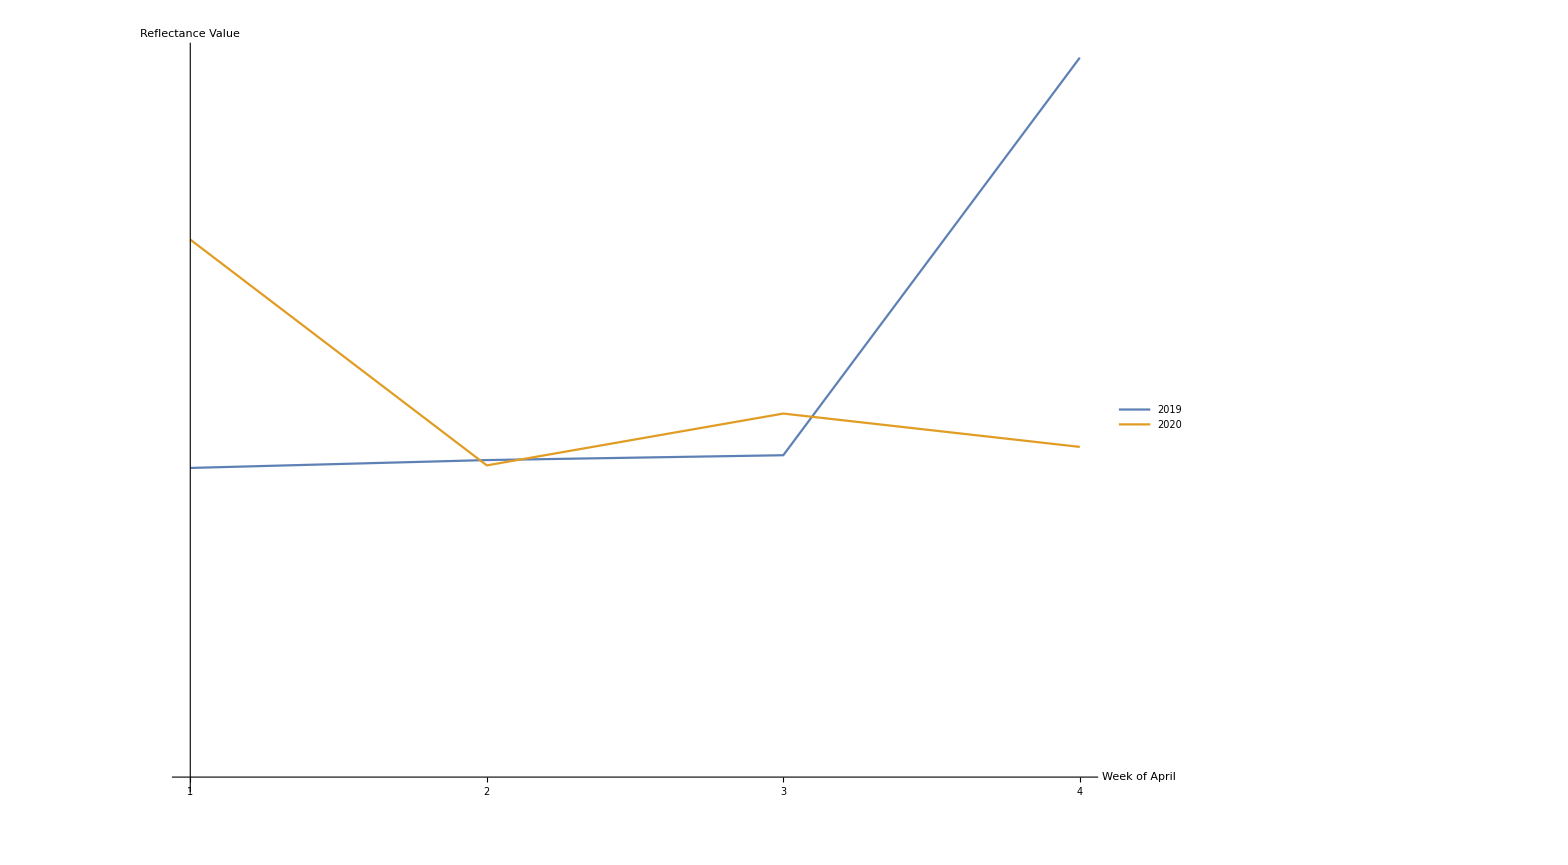

```mathematica
ListLinePlot[{10^-4*Table[meandata[[i]],{i,9,12}],10^-4*Table[meandata[[i]],{i,13,16}]},AxesOrigin->{1,0},PlotLegends->{"2019","2020"},PlotRange->Full,AxesLabel->{"Week of April","Reflectance Value"},LabelStyle->Directive[Bold,FontFamily->"Times New Roman",35],Ticks->{{1,2,3,4},{0.2,0.4,0.6,0.8}},ImageSize->1400,TicksStyle->Large]
```

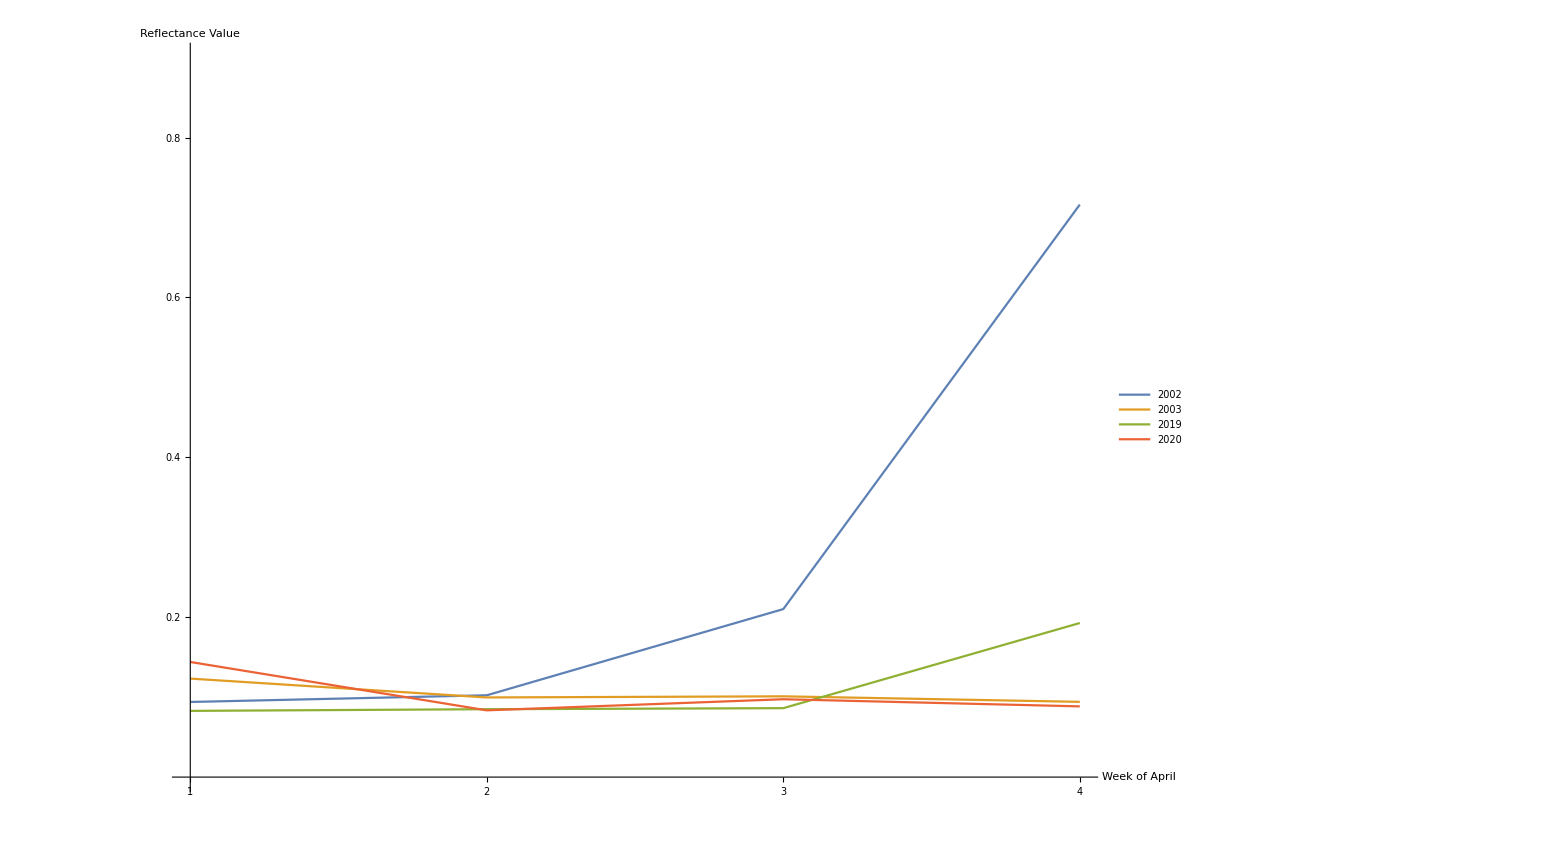

```mathematica
ListLinePlot[{10^-4*Table[meandata[[i]],{i,1,4}],10^-4*Table[meandata[[i]],{i,5,8}],10^-4*Table[meandata[[i]],{i,9,12}],10^-4*Table[meandata[[i]],{i,13,16}]},AxesOrigin->{1,0},PlotLegends->{"2002","2003","2019","2020"},PlotRange->{{1,4},{0,0.9}},AxesLabel->{"Week of April","Reflectance Value"},LabelStyle->Directive[Bold,FontFamily->"Times New Roman",35],Ticks->{{1,2,3,4},{0.2,0.4,0.6,0.8}},ImageSize->1400,TicksStyle->Large]
```